```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=ReadList["test1-sigma=1_0-int.dat"];
l=N[l];
len=Length[l]
```

1048576

```mathematica
Mean[l]
StandardDeviation[N@l]
```

-0.49979

1.04081

{1.,0.822388,0.773714,0.750092,0.731235,0.717735,0.70621,0.697468,0.689204,0.682106,0.67545,0.669814,0.664652,0.659444,0.655494,0.651251,0.646957,0.642923,0.638874,0.636026,0.632962}

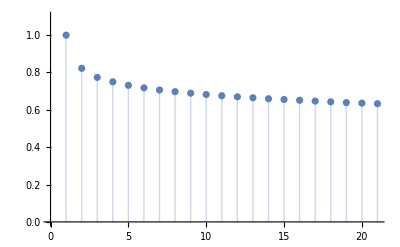

14.744

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```